```mathematica
NotebookEvaluate[NotebookDirectory[]<>"RubiksCube.nb",EvaluationElements->Automatic]
```

## Graphics Primitives

A single cell of a small cube.

```mathematica
cell[center_,number_]:={
{
EdgeForm[Black],
Opacity[1],
White,
Polygon[Transpose[center+Transpose@{{-1,-1},{1,-1},{1,1},{-1,1}}/2]]
},
{
Text[Style[ToString[number],Black,24],center]
}
}
```

Create one single face of the Rubik’s Cube

```mathematica
face[center_,range_List,index_]:=With[{
offsets=Catenate@Outer[{#2,#1}&,{1,0,-1},{-1,0,1}]
},
MapThread[
cell[#1+center,#2]&,
{
offsets,
ReplaceAll[Range[range[[1]],range[[2]]-1],Floor[Plus@@range/2]->index]
}
]
]
```

Create the 2D flatten diagram of the Rubik’s Cube

```mathematica
cubeFlattened=With[{
offsets={{0,3},{-3,0},{0,0},{3,0},{6,0},{0,-3}}
},
MapThread[
face[#1,#2,#3]&,
{
offsets,
Partition[Range[1,55,9],2,1],
{"T","L","F","R","B","D"}
}
]
];
```

Number order and face indices are shown as following:

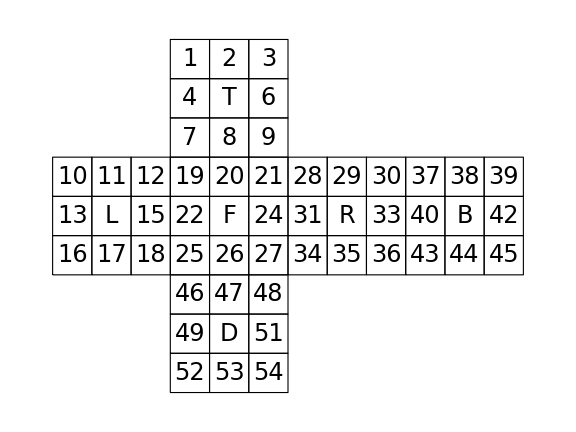

```mathematica
Graphics[cubeFlattened,ImageSize->Large]
```

Each operator is named by corresponding face index, giving a permutation of those numbers.

```mathematica
operators
```

<|T→Cycles[{{1,3,9,7},{2,6,8,4},{10,37,28,19},{11,38,29,20},{12,39,30,21}}],L→Cycles[{{1,19,46,45},{4,22,49,42},{7,25,52,39},{10,12,18,16},{11,15,17,13}}],F→Cycles[{{7,28,48,18},{8,31,47,15},{9,34,46,12},{19,21,27,25},{20,24,26,22}}],R→Cycles[{{3,43,48,21},{6,40,51,24},{9,37,54,27},{28,30,36,34},{29,33,35,31}}],B→Cycles[{{1,16,54,30},{2,13,53,33},{3,10,52,36},{37,39,45,43},{38,42,44,40}}],D→Cycles[{{16,25,34,43},{17,26,35,44},{18,27,36,45},{46,48,54,52},{47,51,53,49}}]|>